## Data

```mathematica
ti={1,5,10,25,50};
```

```mathematica
data0={62.068,63.63,59.96,50.9,40.54};
err0={0.03,0.08,0.11,0.19,0.28};
```

```mathematica
data11={147.747,118.178,102.611,80.63,62.77};
err11={0.01,0.021,0.035,0.07,0.1};
```

```mathematica
ps0={ti/1000,data0}//Transpose;
ps11={ti/1000,data11}//Transpose;
wei0=1/err0^2;
wei11=1/err11^2;
```

```mathematica
eps=10^-8;
```

```mathematica
M=0.938;
m=0.136;
```

```mathematica
Bd=2.224575*10^-3;(*dueteron binding energy*)
Bv=0.066*10^-3;(*1S0 virtual pole*)
```

```mathematica
SElab[ee_]:=2M(2M+ee);
kk[s_]:=(√(s-4 M^2))/2;
```

```mathematica
ρ[s_]:=I(√(4 M^2-s-I eps))/(√(s+I eps));
```

```mathematica
δB[s_,sb_]:=-180/π ArcTan[Re[ρ[s]*√(sb/(4 M^2-sb))]];
δV[s_,sv_]:=180/π ArcTan[Re[ρ[s]*√(sv/(4 M^2-sv))]];
```

## Hu Fit

```mathematica
del1S0[T_,v_,R_,R1_,R2_]:=180/π(-R kk[SElab[T]]+R1 kk[SElab[T]]^3+R2 kk[SElab[T]]^5)+δV[SElab[T],v];
```

```mathematica
del3S1[T_,b_,R_,R1_,R2_]:=180/π(-R kk[SElab[T]]+R1 kk[SElab[T]]^3+R2 kk[SElab[T]]^5)+δB[SElab[T],b]+180;
```

```mathematica
fit0=NonlinearModelFit[ps0,del1S0[t,(2M-xbv)^2,xR/m,R1,R2],{{xbv,Bv},{xR,1.1},{R1,5},{R2,5}},t,Weights->wei0];
```

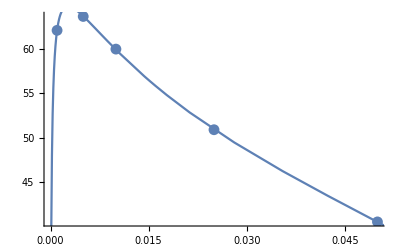

```mathematica
Show[ListPlot[ps0],Plot[fit0[t],{t,0,0.35}]]
```

```mathematica
fit0["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
xbv | 0.0000674211 | 3.55221×10^-7 | {0.0000629076,0.0000719346}
xR | 0.855565 | 0.00491754 | {0.793082,0.918048}
R1 | 72.9206 | 6.97865 | {-15.7515,161.593}
R2 | -1298.48 | 251.792 | {-4497.8,1900.85}

```mathematica
Abs[Bv-0.0000674211]/Bv
```

0.0215318

```mathematica
fit0["ANOVATable"]
```

| DF | SS | MS
Model | 4 | 5.30296×10^6 | 1.32574×10^6
Error | 1 | 0.459785 | 0.459785
Uncorrected Total | 5 | 5.30296×10^6 | 
Corrected Total | 4 | 9924.76 |

```mathematica
fit11=NonlinearModelFit[ps11,del3S1[t,(2M-xbd)^2,xR/m,R1,R2],{{xbd,Bd},{xR,0.8},{R1,5},{R2,5}},t,Weights->wei11];
```

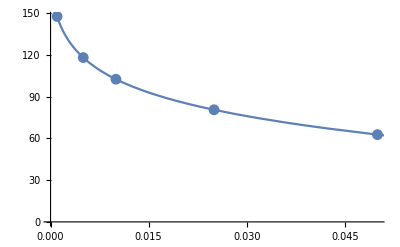

```mathematica
Show[ListPlot[ps11],Plot[fit11[t],{t,0,0.35},PlotRange->All]]
```

```mathematica
fit11["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
xbd | 0.00220319 | 3.22729×10^-6 | {0.00216218,0.00224419}
xR | 0.747903 | 0.00170064 | {0.726294,0.769511}
R1 | 29.5075 | 1.72316 | {7.61262,51.4023}
R2 | -374.54 | 56.2104 | {-1088.76,339.681}

```mathematica
Abs[Bd-0.00220319]/Bd
```

0.00961307

```mathematica
fit11["ANOVATable"]
```

| DF | SS | MS
Model | 4 | 2.60277×10^8 | 6.50692×10^7
Error | 1 | 0.113986 | 0.113986
Uncorrected Total | 5 | 2.60277×10^8 | 
Corrected Total | 4 | 4.09955×10^6 |

```mathematica
kk[SElab[0.05]]
```

0.153134